```mathematica
(*2-mode velocity function:*)
```

```mathematica
v[{x1_, y1_ ,x2_, y2_}] := {(Subscript[μ, 1]+Subscript[a, 1](x1^2 + y1^2) + Subscript[b, 1](x2^2 + y2^2))x1 + Subscript[c, 1](x1 x2 + y1 y2),(Subscript[μ, 1]+Subscript[a, 1](x1^2 + y1^2) + Subscript[b, 1](x2^2 + y2^2))y1 + Subscript[c, 1](x1 y2 - x2 y1),(Subscript[μ, 2]+Subscript[a, 2](x1^2 + y1^2) + Subscript[b, 2](x2^2 + y2^2))x2 + Subscript[c, 2](x1^2 - y1^2) + Subscript[e, 2] y2, (Subscript[μ, 2]+Subscript[a, 2](x1^2 + y1^2) + Subscript[b, 2](x2^2 + y2^2))y2 + 2 Subscript[c, 2] x1 y1 - Subscript[e, 2] x2};
```

```mathematica
(*Paremeters that are 0 or 1*)par01 = {Subscript[μ, 2]-> 1, Subscript[e, 2]-> 1, Subscript[a, 1]-> -1, Subscript[b, 1]-> 0, Subscript[b, 2]-> 0, Subscript[c, 2]-> 1} ;
```

```mathematica
pars = {Subscript[μ, 1]-> -2.8, Subscript[a, 2]-> -2.66, Subscript[c, 1]-> -7.75};
```

```mathematica
vpars[{x1_,y1_,x2_,y2_}] := v[{x1, y1, x2, y2}] /. par01 /. pars
```

```mathematica
x0={0.439966,0,-0.386267,0.070204};
```

```mathematica
(*10.7 - Integrating the two-mode system:*)
```

```mathematica
sol = NDSolve[{{x1sol'[t], y1sol'[t],x2sol'[t], y2sol'[t]  } == vpars[{x1sol[t], y1sol[t], x2sol[t], y2sol[t]}],{x1sol[0], y1sol[0],x2sol[0], y2sol[0] }== x0}, {x1sol,y1sol,x2sol,y2sol}, {t,0,400}, MaxSteps-> ∞, Method-> {"ExplicitRungeKutta", "DifferenceOrder"-> 8}, InterpolationOrder-> All];
```

```mathematica
(*Plot:*)
```

```mathematica
ParametricPlot3D[Evaluate[{x1sol[t], y1sol[t], x2sol[t]}/.sol ], {t,0,400}, PlotPoints-> 4000, Boxed-> False, AxesLabel->{Subscript[x, 1],Subscript[y, 1],Subscript[x, 2]}]
```

-Graphics3D-

```mathematica
(*10A.6 - Invariant subspace of the two-mode system: *)
FullSimplify[v[{0,0, x2, y2}]]
```

{0,0,x2 (x2^2+y2^2) b_2+y2 e_2+x2 μ_2,y2 (x2^2+y2^2) b_2-x2 e_2+y2 μ_2}

```mathematica
(*SO(2) Lie algebra generator:*)
```

```mathematica
T = {{0,1,0,0},{-1,0,0,0},{0,0,0,2},{0,0,-2,0}};
```

```mathematica
(*Phase velocity:*)
vϕ [xRed_] := (v[xRed].(T.xp))/((T.xRed).(T.xp))
```

```mathematica
(*Velocity within the slice:*)
vred[xRed_] := v[xRed] - vϕ[xRed](T.xRed)
```

```mathematica
(*10A.7a - Phase velocity for the 1st mode slice:*)
```

```mathematica
slicep = {1,0,0,0};
```

```mathematica
vϕ1stmode = vϕ[{x1, y1, x2, y2}] /. xp -> slicep //FullSimplify
```

((x2 y1-x1 y2) c_1-y1 ((x1^2+y1^2) a_1+(x2^2+y2^2) b_1+μ_1))/x1

```mathematica
(*Note that numerator = v[[2]]*)
```

```mathematica
(*10A.7b, c, d: Slice hyperplane border: x1=0, d - 2 = 2 dimensional, it is the invariant subspace (x1=0, y1=0), symmetry reduced trajectory cannot cross the slice hpyerplane border*)
```

```mathematica
(*Reduced velocity function:*)
```

```mathematica
vred1stmode = vred[{x1, y1, x2, y2}] /. {xp-> slicep, y1 -> 0} // FullSimplify
```

{x1 (x1^2 a_1+(x2^2+y2^2) b_1+x2 c_1+μ_1),0,x1^2 x2 a_2+x2 (x2^2+y2^2) b_2+x1^2 c_2+y2 (2 y2 c_1+e_2)+x2 μ_2,x1^2 y2 a_2+y2 (x2^2+y2^2) b_2-x2 (2 y2 c_1+e_2)+y2 μ_2}

```mathematica
(*10A.10 - Relative equilibria:*)
```

```mathematica
(*Search for relative equilibria in the invariant subspace:*)
```

```mathematica
vRedInvssp = vred1stmode /. x1 -> 0
```

{0,0,x2 (x2^2+y2^2) b_2+y2 (2 y2 c_1+e_2)+x2 μ_2,y2 (x2^2+y2^2) b_2-x2 (2 y2 c_1+e_2)+y2 μ_2}

```mathematica
Solve[vRedInvssp=={0,0,0,0}, {x2,y2}]//FullSimplify
```

{{x2→0,y2→0},{x2→-(√(-b_2 e_2^2-4 c_1^2 μ_2))/(2 √b_2 c_1),y2→-e_2/(2 c_1)},{x2→(√(-b_2 e_2^2-4 c_1^2 μ_2))/(2 √b_2 c_1),y2→-e_2/(2 c_1)},{x2→(-ⅈ e_2+μ_2)/(2 c_1),y2→-(e_2+ⅈ μ_2)/(2 c_1)},{x2→(ⅈ e_2+μ_2)/(2 c_1),y2→-(e_2-ⅈ μ_2)/(2 c_1)}}

```mathematica
(*We are only interested in the real roots, so the last two are unimportant.*) (*First two non-zero roots correspond to the relative equilibrium that we previously found using Hilbert basis. Slice does the job:*)
```

```mathematica
x2^2 + y2^2 /. {x2->-(√(-Subscript[b, 2] Subscript[e, 2]^2-4 Subscript[c, 1]^2 Subscript[μ, 2]))/(2 √Subscript[b, 2] Subscript[c, 1]),y2->-Subscript[e, 2]/(2 Subscript[c, 1])}//Simplify
```

-μ_2/b_2

```mathematica
(*Search for relative equilibria within the slice:*)
```

```mathematica
vred1stmode[[1]]
```

x1 (x1^2 a_1+(x2^2+y2^2) b_1+x2 c_1+μ_1)

```mathematica
(*We divide out the root x1 = 0 as we know that it corresponds to the invariant subspace:*)
```

```mathematica
f1 = vred1stmode[[1]]
```

x1 (x1^2 a_1+(x2^2+y2^2) b_1+x2 c_1+μ_1)

```mathematica
solx1 = Solve[f1 == 0, x1]//FullSimplify
```

{{x1→0},{x1→-(√(-(x2^2+y2^2) b_1-x2 c_1-μ_1))/(√a_1)},{x1→(√(-(x2^2+y2^2) b_1-x2 c_1-μ_1))/(√a_1)}}

```mathematica
(*We now got a condition on x1^2 for relative equilibria within the slice, we continue by substituting this into the 3rd and 4th velocity components:.*)
```

```mathematica
f3 = vred1stmode[[3]] /. solx1[[3]]//FullSimplify
```

1/a_1(-x2 a_2 ((x2^2+y2^2) b_1+x2 c_1+μ_1)-c_2 ((x2^2+y2^2) b_1+x2 c_1+μ_1)+a_1 (x2 (x2^2+y2^2) b_2+y2 (2 y2 c_1+e_2)+x2 μ_2))

```mathematica
soly2 = Solve[f3==0, y2]//FullSimplify
```

{{y2→(a_1 e_2-√(a_1^2 e_2^2-4 (x2 a_2 b_1-a_1 (x2 b_2+2 c_1)+b_1 c_2) (x2 a_2 (x2 (x2 b_1+c_1)+μ_1)+c_2 (x2 (x2 b_1+c_1)+μ_1)-x2 a_1 (x2^2 b_2+μ_2))))/(2 (x2 a_2 b_1-a_1 (x2 b_2+2 c_1)+b_1 c_2))},{y2→(a_1 e_2+√(a_1^2 e_2^2-4 (x2 a_2 b_1-a_1 (x2 b_2+2 c_1)+b_1 c_2) (x2 a_2 (x2 (x2 b_1+c_1)+μ_1)+c_2 (x2 (x2 b_1+c_1)+μ_1)-x2 a_1 (x2^2 b_2+μ_2))))/(2 (x2 a_2 b_1-a_1 (x2 b_2+2 c_1)+b_1 c_2))}}

```mathematica
f4 = vred1stmode[[4]] /. solx1[[3]]//FullSimplify
```

y2 (x2^2+y2^2) b_2-x2 (2 y2 c_1+e_2)-(y2 a_2 ((x2^2+y2^2) b_1+x2 c_1+μ_1))/a_1+y2 μ_2

```mathematica
(*Try to f3 and f4 for r2sq = x2^2 + y2^2*)
```

```mathematica
f3r2 = f3 /. (x2^2 + y2^2) -> r2sq //FullSimplify
```

1/a_1(-x2 a_2 (r2sq b_1+x2 c_1+μ_1)-c_2 (r2sq b_1+x2 c_1+μ_1)+a_1 (y2 (2 y2 c_1+e_2)+x2 (r2sq b_2+μ_2)))

```mathematica
f4r2 = f4 /. (x2^2 + y2^2) -> r2sq//FullSimplify
```

r2sq y2 b_2-x2 (2 y2 c_1+e_2)-(y2 a_2 (r2sq b_1+x2 c_1+μ_1))/a_1+y2 μ_2

```mathematica
Solve[f3r2 == 0, r2sq]//FullSimplify
```

{{r2sq→(-(x2 a_2+c_2) (x2 c_1+μ_1)+a_1 (y2 (2 y2 c_1+e_2)+x2 μ_2))/(x2 a_2 b_1-x2 a_1 b_2+b_1 c_2)}}

```mathematica
Solve[f4r2 == 0, r2sq]//FullSimplify
```

{{r2sq→(-y2 a_2 (x2 c_1+μ_1)+a_1 (-x2 (2 y2 c_1+e_2)+y2 μ_2))/(y2 (a_2 b_1-a_1 b_2))}}

{{r2sq→(-y2 a_2 (x2 c_1+μ_1)+a_1 (-x2 (2 y2 c_1+e_2)+y2 μ_2))/(y2 (a_2 b_1-a_1 b_2))}}

{{r2sq→(-y2 a_2 (x2 c_1+μ_1)+a_1 (-x2 (2 y2 c_1+e_2)+y2 μ_2))/(y2 (a_2 b_1-a_1 b_2))}}

```mathematica
(*Cannot see any other helpful simplification*)
```

```mathematica
(*Simplify parameters:*)
```

```mathematica
f3simple= f3 /. par01 //FullSimplify
```

x2+y2+(x2+2 y2^2+x2^2 a_2) c_1+(1+x2 a_2) μ_1

```mathematica
f4simple = f4 /. par01 // FullSimplify
```

-x2+y2+x2 y2 (-2+a_2) c_1+y2 a_2 μ_1

```mathematica
solx2simple=Solve[f4simple == 0, x2]
```

{{x2→(-y2-y2 a_2 μ_1)/(-1-2 y2 c_1+y2 a_2 c_1)}}

```mathematica
fy2 = f3simple /. solx2simple[[1]]//FullSimplify
```

1/(-1+y2 (-2+a_2) c_1)^2(y2 (2+c_1 (1+8 y2-2 y2 a_2+y2 (-2+a_2) (-1-6 y2+y2 a_2) c_1+2 y2^3 (-2+a_2)^2 c_1^2))-(-1+y2 a_2 (-2+c_1)-2 y2 c_1) (1+2 y2 c_1) μ_1+y2 a_2^2 (1+2 y2 c_1) μ_1^2)

```mathematica
(*fy2 == 0 corresponds to the solution of a 4th order polynomial, hence the solution is exact.*)
```

```mathematica
(*However, it's long, so at this point, we plug the numbers in and see what we have:*)
```

```mathematica
soly2Num = Solve[fy2 == 0/. pars, y2]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{y2→0.0165355-0.344139 ⅈ},{y2→0.0165355+0.344139 ⅈ},{y2→0.0166195},{y2→0.0702044}}

```mathematica
(*Meaningful solutions are real ones.*)
```

```mathematica
solx2Num = solx2simple /. pars /. soly2Num
```

{{{x2→-0.23331-0.0188013 ⅈ}},{{x2→-0.23331+0.0188013 ⅈ}},{{x2→0.351189}},{{x2→-0.386267}}}

```mathematica
(*Finally, we should check x1^2 for these numbers and find relative equilibria:*)
```

```mathematica
solx1simple = solx1/.par01
```

{{x1→0},{x1→ⅈ √(-x2 c_1-μ_1)},{x1→-ⅈ √(-x2 c_1-μ_1)}}

```mathematica
solx1SimpleNum = solx1simple /. pars
```

{{x1→0},{x1→ⅈ √(2.8+7.75 x2)},{x1→-ⅈ √(2.8+7.75 x2)}}

```mathematica
(*Note, in this case, x1 depends only on x2*)
```

```mathematica
solx1Num =solx1SimpleNum /. solx2Num
```

{{{{x1→0},{x1→0.0729585+0.998584 ⅈ},{x1→-0.0729585-0.998584 ⅈ}}},{{{x1→0},{x1→-0.0729585+0.998584 ⅈ},{x1→0.0729585-0.998584 ⅈ}}},{{{x1→0},{x1→0.+2.34983 ⅈ},{x1→0.-2.34983 ⅈ}}},{{{x1→0},{x1→-0.439966+0. ⅈ},{x1→0.439966+0. ⅈ}}}}

```mathematica
(*We have two physical relative equilibrium (Satisfying x1>0 and x1 ∈ Reals):*)
```

```mathematica
xreqv = Re[({x1, 0, x2, y2} /. solx1Num[[4]][[1]][[3]] /. solx2Num[[4]] /. soly2Num[[4]])[[1]]]
```

{0.439966,0,-0.386267,0.0702044}

```mathematica
(*Let us verify that this is a relative equilibrium by plugging this into the reduced velocity:*)
```

```mathematica
vred1stmode /. par01 /. pars
```

{x1 (-2.8-x1^2-7.75 x2),0,x1^2+x2-2.66 x1^2 x2+(1-15.5 y2) y2,-x2 (1-15.5 y2)+y2-2.66 x1^2 y2}

```mathematica
vRedNum[{x1_,y1_,x2_,y2_}] := {x1 (-2.8-x1^2-7.75 x2),0,x1^2+x2-2.66 x1^2 x2+(1-15.5 y2) y2,-x2 (1-15.5 y2)+y2-2.66 x1^2 y2}
```

```mathematica
vRedNum[xreqv]
```

{0.,0,1.38778×10^-15,-7.63278×10^-17}

```mathematica
(*Seems correct!*)
```

```mathematica
(*Solve the symmetry reduced equations:*)
```

```mathematica
solred = NDSolve[{{x1redsol'[t], y1redsol'[t],x2redsol'[t], y2redsol'[t]} == vRedNum[{x1redsol[t], y1redsol[t], x2redsol[t], y2redsol[t]}],{x1redsol[0], y1redsol[0],x2redsol[0], y2redsol[0] }== x0}, {x1redsol,y1redsol,x2redsol,y2redsol}, {t,0,400}, MaxSteps-> ∞, Method-> {"ExplicitRungeKutta", "DifferenceOrder"-> 8, "StiffnessTest"->False}, InterpolationOrder-> All ];
```

```mathematica
(*Plot reduced trajectory*)
```

```mathematica
redPlot = ParametricPlot3D[Evaluate[{x1redsol[t], x2redsol[t], y2redsol[t]}/.solred ], {t,0,400}, PlotPoints-> 400, Boxed-> False, AxesLabel->{Subscript[x, 1],Subscript[x, 2],Subscript[y, 2]}, BoxRatios->{1,1,1} , PlotRange-> {{0,2.5},{-2.5,1},{-0.5,0.6}}]
```

-Graphics3D-

```mathematica
(*10A.9 - Visualizing the relative equilibrium:*)
```

```mathematica
ParametricPlot3D[{Evaluate[{x1redsol[t], x2redsol[t], y2redsol[t]}/.solred ], Evaluate[{x1sol[t], x2sol[t], y2sol[t]}/.sol ]} , {t,0,250}, PlotPoints-> 500, Boxed-> False, AxesLabel->{Subscript[x, 1],Subscript[x, 2],Subscript[y, 2]}, BoxRatios->{1,1,1} , PlotRange-> Automatic]
```

-Graphics3D-

```mathematica
(*Red -> Symmetry equivariant state space, Blue -> Reduced state space trajectory*)
```

```mathematica
(*10A.10 - Stability of Relative Equilibrium:*)
```

```mathematica
(*Let us start by computing the stability matrix of the 2-mode system in the reduced statespace:*)
```

```mathematica
Ared = IdentityMatrix[4] (*Dummy assignment*);
```

```mathematica
xdummy = {x1,y1,x2,y2};
```

```mathematica
For[i=1, i≤ 4, i++, For[j = 1, j≤ 4, j++, Ared[[i,j]] = D[ vred[xdummy][[i]], xdummy[[j]]]]];
```

```mathematica
Ared = Ared /. xp -> slicep /. par01//FullSimplify
```

{{(-(x1^2+y1^2) (3 x1^2-y1^2-x2 c_1)+(x1-y1) (x1+y1) μ_1)/x1^2,((-2 x2 y1+2 x1 y2) c_1+2 y1 (-2 (x1^2+y1^2)+μ_1))/x1,((x1-y1) (x1+y1) c_1)/x1,2 y1 c_1},{0,0,0,0},{(2 (x1^3-x1^2 y1 y2+y1^3 y2+x1^3 x2 a_2+x2 y1 y2 c_1-y1 y2 μ_1))/x1^2,-2 y1+2 x2 y1 a_2-(2 y2 (x1^2+3 y1^2+x2 c_1-μ_1))/x1,1+(x1^2+y1^2) a_2-(2 y1 y2 c_1)/x1,(x1-2 x1^2 y1-2 y1^3+(-2 x2 y1+4 x1 y2) c_1+2 y1 μ_1)/x1},{(2 (x1^3 y2 a_2+y1 (x1^2 (1+x2)-x2 y1^2+x2 (-x2 c_1+μ_1))))/x1^2,2 (x1+y1 y2 a_2+(x2 (x1^2+3 y1^2+x2 c_1-μ_1))/x1),(-x1+2 x1^2 y1+2 y1^3+(4 x2 y1-2 x1 y2) c_1-2 y1 μ_1)/x1,1+(x1^2+y1^2) a_2-2 x2 c_1}}

```mathematica
(*Note:*)
Ared[[2]]
```

{0,0,0,0}

```mathematica
fAredNum[{xx1_,yy1_,xx2_,yy2_}]:=Ared/.pars /.{x1-> xx1, y1-> yy1, x2-> xx2, y2-> yy2}
```

```mathematica
xreqv
```

{0.439966,0,-0.386267,0.0702044}

```mathematica
λ = Eigenvalues[fAredNum[xreqv]]
```

{-5.50552,0.0507275+2.45275 ⅈ,0.0507275-2.45275 ⅈ,0.}

```mathematica
e = Eigenvectors[fAredNum[xreqv]]
```

{{0.1071,0.,0.160769,0.981164},{0.807165+0. ⅈ,0.+0. ⅈ,-0.103654-0.580624 ⅈ,-0.0247712+0.00172256 ⅈ},{0.807165+0. ⅈ,0.+0. ⅈ,-0.103654+0.580624 ⅈ,-0.0247712-0.00172256 ⅈ},{-2.44216×10^-16,0.488822,-0.156001,-0.858322}}

```mathematica
(*Note, Re[Subscript[λ, 3,4]] > 0, hence the unstable direction:*)
```

```mathematica
unstable = λ[[2]]*e[[2]] + λ[[3]]*e[[3]]
```

{0.0818909+0. ⅈ,0.+0. ⅈ,2.83773+0. ⅈ,-0.0109632+0. ⅈ}

```mathematica
(*This is a real vector:*)
```

```mathematica
unstable = Re[unstable]/Norm[unstable]
```

{0.0288457,0.,0.999576,-0.00386172}

```mathematica
xreqv3D = {xreqv[[1]], xreqv[[3]],xreqv[[4]]}
```

{0.439966,-0.386267,0.0702044}

```mathematica
unstable3D = {unstable[[1]], unstable[[3]], unstable[[4]]}/1.5;
```

```mathematica
sum3D = xreqv3D + unstable3D;
```

```mathematica
redPlot2 = ParametricPlot3D[Evaluate[{x1redsol[t], x2redsol[t], y2redsol[t]}/.solred ], {t,0,400}, PlotPoints-> 400, Boxed-> False, AxesLabel->{Subscript[x, 1],Subscript[x, 2],Subscript[y, 2]}, BoxRatios->{1,1,1} , PlotRange-> {{0,0.90},{-2,0.5},{-0.5,0.6}}];
```

```mathematica
Show[redPlot2, Graphics3D[{Red,Arrow[{xreqv3D,sum3D}]}]]
```

-Graphics3D-

```mathematica
(*Reduced flow, and the unstable direction of the relative equilibrium:*)
```

```mathematica
(*Now let us try to construct a Poincare section that includes this unstable direction vector:*)
```

```mathematica
(*We still have the freedom in the orientation of the Poincare section.*)
```

```mathematica
(*We can choose a normal vector by needing the Poincare section include also the basis in Subscript[y, 2] direction:*)
```

```mathematica
n3D = Cross[{0,0,1}, unstable3D]
```

{-0.999576,0.0288457,0.}

```mathematica
n = {n3D[[1]], 0, n3D[[2]], n3D[[3]]} (*Note: this is a particular choice.*)
```

{-0.999576,0,0.0288457,0.}

```mathematica
(*Now, the condition for being on a Poincare section:*)
```

```mathematica
Poincare[x_] := (x - xreqv).n
```

```mathematica
(*Interpolated function corresponding to the solution in the reduced state space:*)
```

```mathematica
fSolred[t_] := Evaluate[{x1redsol[t],y1redsol[t], x2redsol[t], y2redsol[t]}/.solred ][[1]]
```

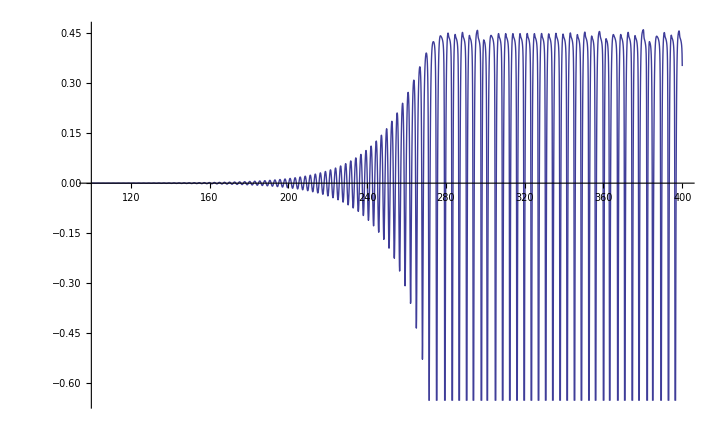

```mathematica
Plot[Poincare[fSolred[t]], {t,100,400}]
```

```mathematica
t00 = 100;
```

```mathematica
tf = 400;
```

```mathematica
Pt = ConstantArray[0, tf-t00] (*Dummy vector*);
```

```mathematica
(*Find time points of Poincare section intersections:*)
```

```mathematica
For[t0 = t00, t0<tf,t0++, Pt[[t0-279]] = t/. FindRoot[Poincare[fSolred[t]],{t,t0}]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

InterpolatingFunction::dmval: Input value {-12.1996} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
Pt = Sort[DeleteDuplicates[Pt]];
```

```mathematica
Psect = ConstantArray[0, {Length[Pt], 4}] (*Dummy matrix to hold the poincare section intersections*);
```

```mathematica
Psect3D = ConstantArray[0, {Length[Pt], 3}] (*Dummy matrix to hold the poincare section intersections (3D)*);
```

```mathematica
PsectRel = ConstantArray[0, {Length[Pt], 3}] (*Dummy matrix to hold the relative poincare section coordinates (3D)*);
```

```mathematica
For[i = 1, i< Length[Pt], i++, {Psect[[i]] = fSolred[Pt[[i]]], Psect3D[[i]] ={fSolred[Pt[[i]]][[1]], fSolred[Pt[[i]]][[3]], fSolred[Pt[[i]]][[4]]}, PsectRel[[i]] = Psect3D[[i]] - xreqv3D}];
```

```mathematica
PsectPlot=ListPointPlot3D[Psect3D, PlotStyle-> {Pink}]
```

-Graphics3D-

```mathematica
Show[redPlot2, Graphics3D[{Red,Arrow[{xreqv3D,sum3D}]}], PsectPlot]
```

-Graphics3D-

```mathematica
(*Now let's project to the basis on the Poincare section. It's done by the following transformation matrix:*)
```

```mathematica
U = {unstable3D,{0,0,1} , n3D}
```

{{0.0192304,0.666384,-0.00257448},{0,0,1},{-0.999576,0.0288457,0.}}

```mathematica
(*Relative coordinates of the Poincare section:*)
```

```mathematica
PsectProj = U.Transpose[PsectRel];
```

```mathematica
Psect2D = Transpose[PsectProj[[Range[2]]]];
```

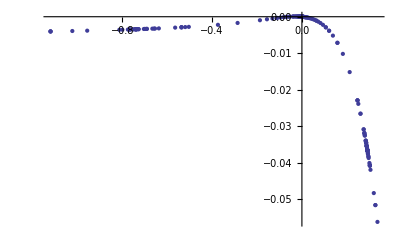

```mathematica
ListPlot[Psect2D]
```